```mathematica
dir=NotebookDirectory[];
```

```mathematica
folders=StringSplit[#,"\\"][[-1]]&/@Select[FileNames[All,dir],DirectoryQ];
PopupMenu[Dynamic[folder],folders,MenuStyle->{16,"Black"}]
```

```mathematica
fileNames=FileNames[FileNameJoin[{dir,folder,"*.xlsx"}]];
fileChoices=Table[fileNames⟦i⟧->FileNameTake[fileNames⟦i⟧],{i,1,Length[fileNames]}];
PopupMenu[Dynamic[fileImport],fileChoices,MenuStyle->{16,"Black"}]
```

```mathematica
repeats=1;
conc=Table[{0,0.1,0.25,0.5,1,2.5,5,10},{i,1,repeats}];
```

```mathematica
proteinDilution=10; (*protein dilution factor before addition to 100μl well*)
proteinConc=4.56/proteinDilution; (*mg·ml^-1 from bradford*)
lysateDilutionInWell=100/20; (*20μl in 100μl assay*)
pathLength=0.26; (*10μl well volume*)
NADHExt=6.22 (*mM^-1 cm^-1*);
```

```mathematica
rangeCheck[r_]:=Module[{},Manipulate[range[r]={p⟦1⟧,q⟦1⟧};Show[dataPlots⟦r⟧,Epilog->{Gray,Opacity[0.2],Rectangle[{p⟦1⟧,-1},{q⟦1⟧,2}]}],{{p,{0,0}},Locator,Appearance->None},{{q,{data⟦1,-1,1⟧,0}},Locator,Appearance->None}]]
```

```mathematica
Quiet[Table[rangeCheck[i],{i,Length[dataPlots]}]]
```

{,,,,,,,}

```mathematica
rangeFolder="linearRanges";
```

|

```mathematica
If[oldRanges==0,ranges=Table[range[i],{i,1,Length[dataPlots]}],ranges=Import[FileNameJoin[{dir,folder,rangeFolder,rangeFileName}]]]
```

{{0,1.19},{0.51,2.63},{0,3.29},{0.45,2.97},{0.25,3.45},{0.74,3.89},{0.77,3.96},{0.78,3.8}}

```mathematica
rates=-Table[D[fits[[i]][x],x],{i,1,Length[fits]}]*(proteinDilution/(NADHExt*pathLength*proteinConc))
```

{2.26088,2.26089,2.02981,1.89932,1.73935,1.46757,0.942315,0.361286}

```mathematica
(*Export[FileNameJoin[{dir,folder,rangeFolder,rangeFileName}],ranges]*)
```

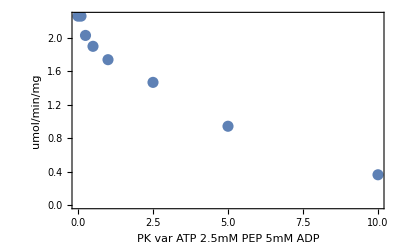

PK var ATP 2.5mM PEP 5mM ADP | 
mM | V (umol/min/mg)
0 | 2.26088
0.1 | 2.26089
0.25 | 2.02981
0.5 | 1.89932
1 | 1.73935
2.5 | 1.46757
5 | 0.942315
10 | 0.361286

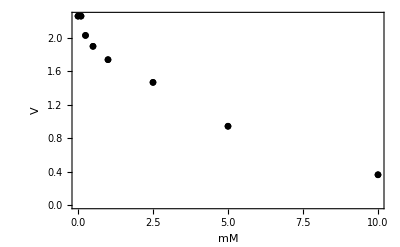

```mathematica
Pane[
,
Full,Alignment->Center]
```

### Data formatting:

```mathematica
allDataHeadings={{"PEP","ADP","Pyr","ATP","F16BP","V(umol/min/mg)"}}
```

{{PEP,ADP,Pyr,ATP,F16BP,V(umol/min/mg)}}

#### vary PEP

```mathematica
(*dataFormatted={#[[1]],5,0,0,0,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary ADP:

```mathematica
(*dataFormatted={2.5,#[[1]],0,0,0,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary Pyr:

```mathematica
(*dataFormatted={10,2,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary ATP:

```mathematica
(*dataFormatted={2.5,5,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary F16BP:

```mathematica
(*dataFormatted={2.5,5,0,#[[1]],#[[2]]}&/@rateData*)
```

#### For Exporting

```mathematica
rateFolder = "outputRates";
rateFileName = StringDelete[fileName,{".xlsx"," "}]<>".csv";
(*Export[FileNameJoin[{dir,folder,rateFolder,rateFileName}],Join[allDataHeadings,dataFormatted]];*)
```